```mathematica
(*test*)
```

```mathematica
Clear[a,b]
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Peter\Documents\Physik\FP2\Moessbauer\code

```mathematica
x={3.01,1.00,0.21,1.95,7.97,0.46,0.66,0.88,1.22,1.43,1.67,1.87,2.16,2.51,3.99,4.98,6.49,9.43,10.92,12.43 };
names={"3.01","1.00","0.21","1.95","7.97","0.46","0.66","0.88","1.22","1.43","1.67","1.87","2.16","2.51","3.99","4.98","6.49","9.43","10.92","12.43"};
```

```mathematica
files=Flatten[Import[StringJoin["../data/background/",#,"mm.TKA"],"CSV"]]&/@names;
```

```mathematica
Dimensions[files]
```

{20,2048}

```mathematica
data=Table[{x[[j]],Sum[files[[j]][[90;;250]][[i]],{i,1,161}]/600.},{j,1,Length[files]}];
```

```mathematica
data
```

{{3.01,27.15},{1.,30.9767},{0.21,40.5283},{1.95,28.14},{7.97,22.9767},{0.46,36.6067},{0.66,33.8917},{0.88,32.3133},{1.22,30.1483},{1.43,29.4067},{1.67,28.8},{1.87,28.285},{2.16,28.285},{2.51,27.7583},{3.99,25.905},{4.98,25.19},{6.49,23.9783},{9.43,21.7483},{10.92,20.3483},{12.43,19.925}}

```mathematica
liplot=ListPlot[data];
```

```mathematica
errordata=Table[{data[[i]],ErrorBar[Sqrt[data[[i]][[2]]/Sqrt[600.]]]},{i,1,Length[data]}];
```

```mathematica
errliplot= ErrorListPlot[errordata,PlotStyle->PointSize[0]];
```

```mathematica
?ErrorListPlot
```

RowBox[{"ErrorListPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TI"]}], "}"}], "]"}] plots points corresponding to a list of values RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", " ", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", " ", StyleBox["…", "TR"]}], with corresponding error bars. The errors have magnitudes RowBox[{SubscriptBox[StyleBox["dy", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}].
RowBox[{"ErrorListPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"ErrorBar", "[", SubscriptBox[StyleBox["err", "TI"], "1"], "]"}]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", RowBox[{"ErrorBar", "[", SubscriptBox[StyleBox["err", "TI"], StyleBox["2", "TR"]], "]"}]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots points with specified StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates and error magnitudes.

```mathematica
model = a Exp[-b v]+c Exp[-d v];
```

```mathematica
nlm= NonlinearModelFit[data, model, {a,b,c,d}, v];
nlm["BestFit"]
```

16.5109 ⅇ^(-1.86792 v)+29.738 ⅇ^(-0.0331478 v)

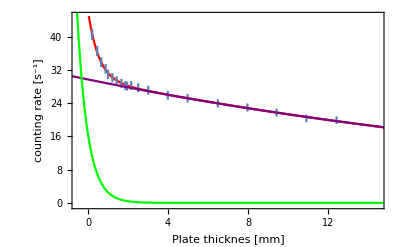

```mathematica
fit=Plot[nlm["BestFit"],{v,-1,15}, PlotStyle->Red,ImageSize-> Medium,PlotRange->{{-0.5,14.5},{-0.5,45}},Frame-> True,FrameLabel-> {"Plate thicknes [mm]","counting rate [s^-1]"}];
datapart=Plot[16.5109*Exp[-1.86792*v],{v,-1,15},PlotRange->All,PlotStyle->Green];
comptonpart=Plot[29.738*Exp[-0.0331478*v],{v,-1,15},PlotRange->All,PlotStyle->Purple];
Show[{fit,errliplot,comptonpart,datapart},ImageSize->Full,FrameStyle->{Thick,Black},LabelStyle->{FontSize->18,Bold,Black}]
```

```mathematica
nlm["CorrelationMatrix"]//MatrixForm
```

(1. | 0.862715 | 0.111216 | 0.761803
0.862715 | 1. | 0.0425748 | 0.596468
0.111216 | 0.0425748 | 1. | 0.614734
0.761803 | 0.596468 | 0.614734 | 1.)

```mathematica
nlm[0](*Extrapoliere Untergrund*)
```

46.249

```mathematica
nplates={1,1,1,1,2,2,3,4,2,3,2,3,2,1,1,2,2,3,4,4};
yerror=Sqrt[#]/600&/@Table[Sum[files[[j]][[90;;250]][[i]],{i,1,161}],{j,1,Length[files]}];
```

```mathematica
exporttable=Table[Join[data[[i]],{Sqrt[nplates[[i]]]*0.01,yerror[[i]]}],{i,1,Length[files]}]//N;
```

```mathematica
Export["../data/background/data.csv",exporttable,"Table"];
```

```mathematica
test
```

test

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 29.738 | 0.167922 | 177.094 | 8.97649×10^-28
b | 0.0331478 | 0.000877251 | 37.786 | 4.48947×10^-17
c | 16.5109 | 0.444221 | 37.1683 | 5.82781×10^-17
d | 1.86792 | 0.0865246 | 21.5884 | 2.93614×10^-13